## Simple Task 6 Valerie Richmond CPS/Math 371 8am

1.

```mathematica
(*The Module sums the cost values associated with a given name in the given list. A loop goes through all elements of the list and, if the name in that element is the same as the given one, adds the cost to the sum, then returns the final sum.*)

purchases[listValues_, sumName_] :=Module[{list=listValues, sum=0, name=sumName, count}, 
For[count=1, count≤Length[list], count++, 
If[list[[count,1]]==name, sum=sum+list[[count, 2]] ]
]; 
Return[sum]
]
```

```mathematica
lst={{"claus", 13.2}, {"tim", 2.45},{"claus", 24.99}, {"april", 19.45}};
```

```mathematica
purchases[lst, "uta"]
purchases[lst, "claus"]
purchases[lst, 3123]
purchases[lst, "april"]
```

0

38.19

0

19.45

2.

```mathematica
(*This Module outputs a graph modeling the path of a notorious drunk, Jon Smitty. A list of points is constructed, with the first having an x of 0 and a given start y. Then, for every successive point, x is incremented by 1 and a random number is generated to determine whether y is increased or decreased by 1. As many steps are generated as the given length, then the list of points is plotted.*)

drunkwalk[ystart_, length_] := Module[{y=ystart,long=length,count, int,list={}, point={}, point1},
point1={0, y};
AppendTo[list, point1];
For[count=1, count≤long, count++, 
AppendTo[point, count];
int= RandomInteger[{0,1}]; 
If[int==0, AppendTo[point  , y+1];y=y+1, AppendTo[point, y-1];y=y-1]; 
AppendTo[list, point];
 point={}
];
Show[ListPlot[list,Joined->True, PlotStyle-> Green, AxesLabel->{"time","height"}]]
]
```

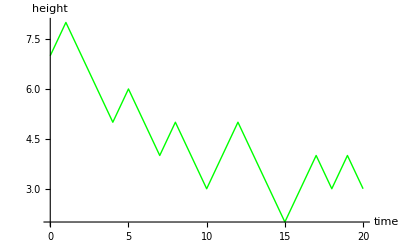

```mathematica
drunkwalk[7,20]
```

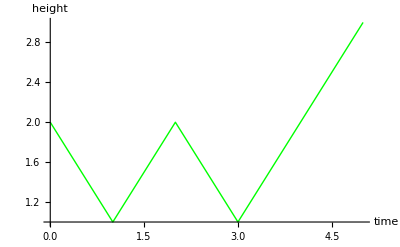

```mathematica
drunkwalk[2, 5]
```